```mathematica
ℏ=4.135667696*10^(-15); (*eV s*)
c=3*10^8 (*m/s*)
ϵ0=8.854187817*10^(-12) (*F/m*)
```

300000000

8.85419×10^-12

### Coefientes de Mie

```mathematica
ψn[n_,ρ_]:= ρ*SphericalBesselJ[n,ρ]
```

```mathematica
ξn[n_,ρ_]:=ρ*SphericalHankelH1[n,ρ]
```

```mathematica
dψn[n_,ρ_]:=SphericalBesselJ[n-1,ρ]-(n+1)/ρ SphericalBesselJ[n,ρ]
dξn[n_,ρ_]:=0.5*(SphericalHankelH1[n-1,ρ]-(SphericalHankelH1[n,ρ]+ρ SphericalHankelH1[n+1,ρ])/ρ)
```

```mathematica
mieCoefAn[np_,nm_,a_,ℏω_,n_]:=Module[{m,ω,λ,x,an},
						m=np/nm;
						ω=ℏω/ℏ;
						λ=2 Pi c/ω;
						x=(2 Pi nm a)/λ;							
						an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x])); 
						an]
```

```mathematica
mieCoefAn[1,1.33,30*10^(-9),1,10]
```

3.83872×10^-102+1.95927×10^-51 ⅈ

```mathematica
mieCoefBn[np_,nm_,a_,ℏω_,n_]:=Module[{m,ω,λ,x,bn},
						m=np/nm;
						ω=ℏω/ℏ;
						λ=2 Pi c/ω;
						x=(2 Pi nm a)/λ;								
						bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
						bn]
```

### Secciones transversales sin Drude

```mathematica
mieCsca[np_,nm_,a_,ℏω_,nmax_]:=Module[{ω,λ,k,Csca},
								ω=ℏω/ℏ;
								λ=2 Pi c/ω;
								k=2 Pi nm/λ;
				Csca =(2 Pi)/k^2 Sum[(2 n +1)(Norm[mieCoefAn[np,nm,a,ℏω,n]^2+Norm[mieCoefBn[np,nm,a,ℏω,n]]]^2),{n,1,nmax}]]
```

```mathematica
mieCext[np_,nm_,a_,ℏω_,nmax_]:=Module[{ω,λ,k,Cext},
								ω=ℏω/ℏ;
								λ=2 Pi c/ω;
								k=2 Pi nm/λ;
Cext =(2 Pi)/k^2 Sum[(2 n +1)Re[(mieCoefAn[np,nm,a,ℏω,n]+mieCoefBn[np,nm,a,ℏω,n])],{n,1,nmax}]]
```

```mathematica
Qsca[np_,nm_,a_,ℏω_,nmax_]:=1/(Pi* a^2) mieCsca[np,nm,a,ℏω,nmax]
```

```mathematica
Qext[np_,nm_,a_,ℏω_,nmax_]:=1/(Pi* a^2) mieCext[np,nm,a,ℏω,nmax]
```

```mathematica
Plot[{Qsca[1,1.33,30*10^(-9),ℏω,100],Qext[1,1.33,30*10^(-9),ℏω,100]},{ℏω,0.1,1},PlotRange->Full,PlotLabels->"Expressions"]
```

General::munfl: (2.39669×10^-206+1.54812×10^-103 ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.18305×10^-222+1.78411×10^-111 ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (3.26359×10^-238+1.80654×10^-119 ⅈ)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

## Modelo de Drude

```mathematica
ϵ[ℏω_,ωp_,γ_]:=Module[{ω=ℏω/ℏ},1-(ωp^2/(ω(ω+I γ)))]
```

```mathematica
ϵ[1,4.3,0.15/ℏ]^2
```

1.+2.35032×10^-30 ⅈ

### Coefientes de Mie

```mathematica
drudemieCoefAn[nm_,a_,ℏω_,ℏωp_,ℏγ_,n_]:=Module[{ω,ωp,γ,ϵ,np,m,λ,x,an},
						ω=ℏω/ℏ;
						ωp=ℏωp/ℏ;
						γ=ℏγ/ℏ;
						ϵ=1-(ωp^2/(ω(ω+I γ)));
						np=Sqrt[ϵ];
						m=np/nm;
						λ=2 Pi c /ω;
						x=(2 Pi nm a)/λ;							
						an=((m ψn[n,m x] dψn[n,x])-(ψn[n,x] dψn[n,m x]))/((m ψn[n,m x] dξn[n,x])-(ξn[n,x] dψn[n,m x])); 
						an]
```

```mathematica
drudemieCoefBn[nm_,a_,ℏω_,ℏωp_,ℏγ_,n_]:=Module[{ω,ωp,γ,ϵ,np,m,λ,x,bn},
						ω=ℏω/ℏ;
						ωp=ℏωp/ℏ;
						γ=ℏγ/ℏ;
						ϵ=1-(ωp^2/(ω(ω+I γ)));
						np=Sqrt[ϵ];
						m=np/nm;
						λ=2 Pi c /ω;
						x=(2 Pi nm a)/λ;							
						bn=((ψn[n,m x] dψn[n,x])-(m ψn[n,x] dψn[n,m x]))/((ψn[n,m x] dξn[n,x])-(m ξn[n,x] dψn[n,m x]));
						bn]
```

### Secciones transversales con Drude

```mathematica
drudeMieCsca[nm_,a_,ℏω_,ℏωp_,ℏγ_,nmax_]:=Module[{ω,ωp,γ,ϵ,np,m,λ,k,Csca},
											ωp=ℏωp/ℏ;
											γ=ℏγ/ℏ;
											ω=ℏω/ℏ;
											ϵ=1-(ωp^2/(ω(ω+I γ)));
											np=Sqrt[ϵ];
											m=np/nm;
											λ=2 Pi c /ω;
											k=2 Pi np/λ;
		Csca =(2 Pi)/k^2 Sum[(2 n +1)(Norm[drudemieCoefAn[np,a,ℏω,ℏωp,ℏγ,n]]^2+Norm[drudemieCoefBn[np,a,ℏω,ℏωp,ℏγ,n]]^2),{n,1,nmax}]]
```

```mathematica
drudeMieCsca[1.33,30*10^(-9),1,4.3,1.5,50]
```

General::munfl: (1.7265×10^-158)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.26886×10^-163)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-3.93436×10^-49-7.16008×10^-49 ⅈ

```mathematica
drudeMieCext[nm_,a_,ℏω_,ℏωp_,ℏγ_,nmax_]:=Module[{ω,ωp,γ,ϵ,np,m,λ,k,Cext},
											ωp=ℏωp/ℏ;
											γ=ℏγ/ℏ;
											ω=ℏω/ℏ;
											ϵ=1-(ωp^2/(ω(ω+I γ)));
											np=Sqrt[ϵ];
											m=np/nm;
											λ=2 Pi c /ω;
											k=2 Pi nm/λ;
Cext =(2 Pi)/k^2 Sum[(2 n +1)Re[(drudemieCoefAn[nm,a,ℏω,ℏωp,ℏγ,n]+drudemieCoefBn[nm,a,ℏω,ℏωp,ℏγ,n])],{n,1,nmax}]]
```

```mathematica
drudeQsca[nm_,a_,ℏω_,ℏωp_,ℏγ_,nmax_]:=1/(Pi* a^2) drudeMieCsca[nm,a,ℏω,ℏωp,ℏγ,nmax]
```

```mathematica
drudeQext[nm_,a_,ℏω_,ℏωp_,ℏγ_,nmax_]:=1/(Pi* a^2) drudeMieCext[nm,a,ℏω,ℏωp,ℏγ,nmax]
```

```mathematica
drudeQsca[1.33,30*10^(-9),1,4.3,1.5,50]
```

General::munfl: (1.7265×10^-158)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.26886×10^-163)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-1.3915×10^-34-2.53236×10^-34 ⅈ

General::munfl: (-1.33446×10^-156+1.32761×10^-156 ⅈ) (9.59445×10^-151+9.64162×10^-151 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

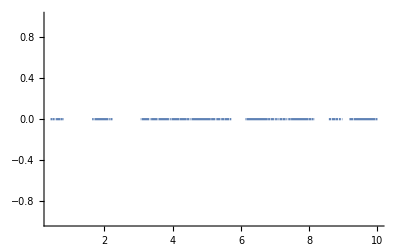

```mathematica
Plot[{drudeQsca[1,30*10^(-9),ℏω,4.3,1.5,50]},{ℏω,0,10},PlotRange->Full]
```

```mathematica
(3+4I)^2
```

-7+24 ⅈ

```mathematica
(3+4I)*(3-4I)
```

25